### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

### 巡回セールスマン問題

```mathematica
Pin={{-1.55,0.52},{1.14,-0.36},{-0.97,-1.31},{0,1.65},{0.97,-1.31},{1.55,0.52},
{-1.46,-2},{0,2.47},{-0.5,-0.15},{-0.31,0.432},{1.46,-2},{2.35,0.78},{0.5,-0.15},
{-1.14,-0.36},{-0.7,0.97},{-2.35,0.78},{0,-0.5},{0.31,0.432},{0,-1.2},{0.7,0.97}};(*Point input*)
```

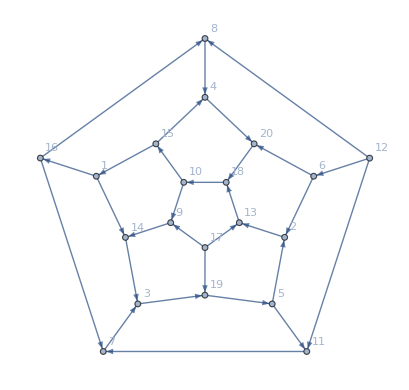

```mathematica
Gin=DirectedGraph[PolyhedronData["Dodecahedron","Skeleton"],"Random",VertexLabels->"Name"](*Ggraph input*)
```

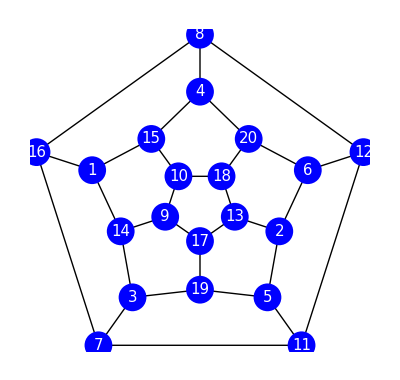

```mathematica
Graphics[{Thick,Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]
}]
```

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,-1},{0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,1,0},{-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,-1,0,-1,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,1,-1,0,0,0,0,0,-1,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,1,0,0,0,0,0,0},{0,-1,-1,0,0,0,0,0,0,0,1,1,0,0,-1,-1,0,0,1,-1,0,0,0,0,0,0,0,0,0,0},{1,0,-1,0,0,0,0,1,1,0,0,0,1,1,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,-1,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{1,0,-1,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,-1,0,0,0,0,-1,-1,0,0,0,1,0,0,0,0,0,0,0,-1,-1,0,0,-1,0,0},{-1,-1,0,-1,0,-1,0,-1,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,-1,0,0,-1,0,0}}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{0.970824,0.961769,0.84119,0.965091,0.970824,0.673573,0.846286,0.965091,0.976217,0.82,0.97591,0.97591,0.846286,0.976217,0.84119,0.961769,2.92,2.91899,2.89458,2.89458,0.612229,0.673573,0.610328,0.664488,0.62,2.91899,0.610328,0.612229,0.7,0.664488}

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{0.970824,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.961769,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.84119,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.965091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.970824,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.673573,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.846286,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.965091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.976217,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.82,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.97591,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.97591,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.846286,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.976217,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.84119,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.961769,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.91899,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.89458,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.89458,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.612229,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.673573,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.610328,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.664488,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.62,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.91899,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.610328,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.612229,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.7,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.664488}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[FundLoop[[i]]][[1]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Point *)
```

{{{0.7,0.97},{0,1.65},{-0.7,0.97},{-0.31,0.432},{0.31,0.432}},{{0,-1.2},{-0.97,-1.31},{-1.14,-0.36},{-0.5,-0.15},{0,-0.5}},{{0,-0.5},{-0.5,-0.15},{-1.14,-0.36},{-1.55,0.52},{-0.7,0.97},{-0.31,0.432},{0.31,0.432},{0.5,-0.15}},{{2.35,0.78},{0,2.47},{-2.35,0.78},{-1.46,-2},{1.46,-2}},{{-0.31,0.432},{-0.7,0.97},{-1.55,0.52},{-1.14,-0.36},{-0.5,-0.15}},{{2.35,0.78},{0,2.47},{-2.35,0.78},{-1.55,0.52},{-0.7,0.97},{0,1.65},{0.7,0.97},{1.55,0.52}},{{1.46,-2},{-1.46,-2},{-2.35,0.78},{-1.55,0.52},{-1.14,-0.36},{-0.97,-1.31},{0,-1.2},{0.97,-1.31}},{{0,2.47},{-2.35,0.78},{-1.55,0.52},{-0.7,0.97},{0,1.65}},{{-1.46,-2},{-2.35,0.78},{-1.55,0.52},{-1.14,-0.36},{-0.97,-1.31}},{{1.55,0.52},{0.7,0.97},{0,1.65},{-0.7,0.97},{-0.31,0.432},{0.31,0.432},{0.5,-0.15},{1.14,-0.36}},{{0.97,-1.31},{0,-1.2},{-0.97,-1.31},{-1.14,-0.36},{-1.55,0.52},{-0.7,0.97},{-0.31,0.432},{0.31,0.432},{0.5,-0.15},{1.14,-0.36}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}<0,1,-1],
{i,Length[FundLoop]}](* 右回りならば正、左回りならば負 *)
```

{-1,1,-1,-1,-1,-1,1,-1,1,1,-1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[FundLoop[[i]]][[1]]]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Area *)
```

{1.01938,1.0336,1.65667,14.5633,1.01025,3.497,3.5481,1.7485,1.7647,2.02963,3.72387}

```mathematica
U=Table[-LoopSpin[[i]]FLA[[i]],{i,Length[FundLoop]}](* 誘導起電力行列(誘導起電力は-B'Sに右回りなら1を、左回りなら-1をかける) *)
```

{1.01938,-1.0336,1.65667,14.5633,1.01025,3.497,-3.5481,1.7485,-1.7647,-2.02963,3.72387}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{0.0845769,0.0850285,0.000451656,-2.23277,2.22658,-0.00619285,-0.0802118,0.00311796,-0.0770939,0.079931,-0.00387292,0.0760581,1.47688,-0.755892,1.47761,-0.748967,-0.737056,0.656844,0.736323,-0.656392,-1.20473,-0.0814589,1.12327,0.0811556,-1.12357,-2.21393,-0.444468,-0.450661,-0.678799,-0.672909}

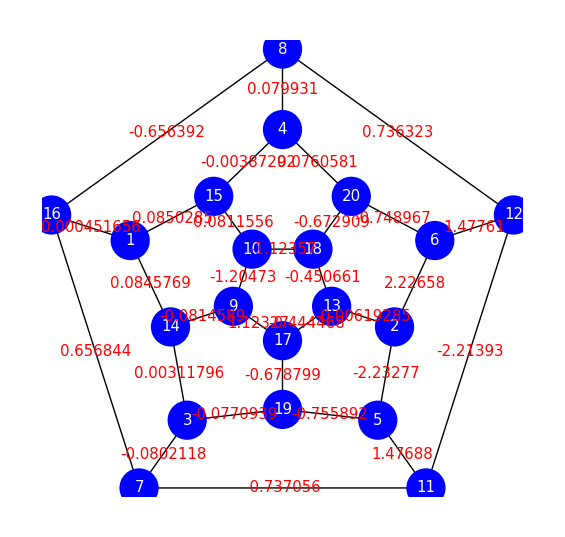

```mathematica
Graphics[{Thick,Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Curr[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
Sort[Abs[Curr],Greater]
```

{2.23277,2.22658,2.21393,1.47761,1.47688,1.20473,1.12357,1.12327,0.755892,0.748967,0.737056,0.736323,0.678799,0.672909,0.656844,0.656392,0.450661,0.444468,0.0850285,0.0845769,0.0814589,0.0811556,0.0802118,0.079931,0.0770939,0.0760581,0.00619285,0.00387292,0.00311796,0.000451656}

FindShortestTour::ngen: The generalized FindShortestTour[Graph[<20>, <30>]] is not implemented.

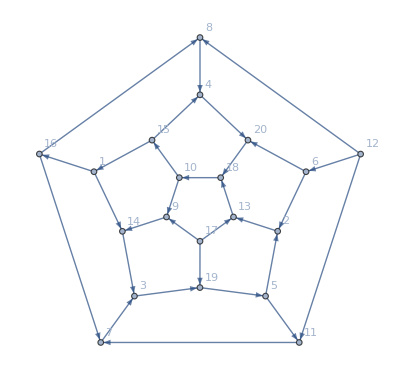
FindShortestTour[-Graphics-]

```mathematica
FindShortestTour[Gin]
```

```mathematica
Graphics[Line[Pin[[Last[%]]]]]
```

Part::pkspec1: The expression … cannot be used as a part specification.

-Graphics-